```mathematica
α[k_]:=KroneckerProduct[PauliMatrix[1],PauliMatrix[k]]
γ[0]=DiagonalMatrix[{1,1,-1,-1}];
```

```mathematica
Clear[ψ,diracEquation1D,m,ℏ,c]
ψ[x_,t_]:={ψs[x,t,1], ψs[x,t,2]}

ℏ=c=1;
diracEquation1D[x_,t_]:= (ⅈ ℏ D[ψ[x,t],t] == -ⅈ ℏ PauliMatrix[1].(D[ψ[x,t],x]) c +m c^2 PauliMatrix[3].ψ[x,t])
hamiltonian[p_,m_]:= PauliMatrix[1]p c + m c^2 PauliMatrix[3]
```

```mathematica
Clear[vals,vecs]
{vals[p_,m_],vecs[p_,m_]}=Eigensystem[hamiltonian[p,m]]//FullSimplify;
(*vecs[p_,m_]=Table[Normalize[v],{v,vecs[p,m]}];*)
```

```mathematica
Clear[projs]
projs[l_,p_,m_]:=FullSimplify[ComplexExpand[PseudoInverse[{vecs[p,m][[l]]}]].{vecs[p,m][[l]]}]
Table[MatrixForm[projs[l,p,m]//FullSimplify],{l,2}]
```

{(1/2-m/(2 √(m^2+p^2)) | -p/(2 √(m^2+p^2))
-p/(2 √(m^2+p^2)) | 1/2 (1+m/(√(m^2+p^2)))),(1/2 (1+m/(√(m^2+p^2))) | p/(2 √(m^2+p^2))
p/(2 √(m^2+p^2)) | 1/2-m/(2 √(m^2+p^2)))}

```mathematica
Clear[ψ0]
ψ0[x0_,σ_]:=(1/(8 σ^2 π))^(1/4)Exp[-x0^2/(4 σ^2)]{1,1}
(*ψ0[x0_,σ_]:=(1/(32 π))^(1/4)Exp[-x0^2/16]{1,1}*)
ψ0F[p_,σ_]=FourierTransform[ψ0[x,σ],x,p];
```

```mathematica
vecs[p,m][[1]]-hamiltonian[p,m].vecs[p,m][[1]]/vals[p,m][[1]]//FullSimplify
vecs[p,m][[2]]-hamiltonian[p,m].vecs[p,m][[2]]/vals[p,m][[2]]//FullSimplify
```

{0,0}

{0,0}

```mathematica
ψ0[x0,1]
ψ0F[p,1]
```

{(ⅇ^(-x0^2/4))/(2^(3/4) π^(1/4)),(ⅇ^(-x0^2/4))/(2^(3/4) π^(1/4))}

{(ⅇ^(-p^2))/(2 π)^(1/4),(ⅇ^(-p^2))/(2 π)^(1/4)}

```mathematica
NIntegrate[Norm[ψ0[x0,2]]^2,{x0,-∞,∞}]
NIntegrate[Norm[ψ0F[p,2]]^2,{p,-∞,∞}]
```

1.

1.

```mathematica
Clear[u]
u[l_,p_,m_,x_,t_]:=1/(√(2π))vecs[p,m][[l]] ⅇ^(ⅈ p x-ⅈ vals[p,m][[l]]t)
```

```mathematica
u[1,p,m,x,t]-hamiltonian[p,m].u[1,p,m,x,t]/vals[p,m][[1]]//FullSimplify
u[2,p,m,x,t]-hamiltonian[p,m].u[2,p,m,x,t]/vals[p,m][[2]]//FullSimplify
```

{0,0}

{0,0}

```mathematica
ψ0F[p,σ]
```

{(ⅇ^(-p^2 σ^2))/((2 π)^(1/4) (1/σ^2)^(1/4)),(ⅇ^(-p^2 σ^2))/((2 π)^(1/4) (1/σ^2)^(1/4))}

```mathematica
projs[2,p,m].ψ0F[p,σ]
```

{(ⅇ^(-p^2 σ^2) p)/(2 √(m^2+p^2) (2 π)^(1/4) (1/σ^2)^(1/4))+(ⅇ^(-p^2 σ^2) (1+m/(√(m^2+p^2))))/(2 (2 π)^(1/4) (1/σ^2)^(1/4)),(ⅇ^(-p^2 σ^2) p)/(2 √(m^2+p^2) (2 π)^(1/4) (1/σ^2)^(1/4))+(ⅇ^(-p^2 σ^2) (1/2-m/(2 √(m^2+p^2))))/((2 π)^(1/4) (1/σ^2)^(1/4))}

```mathematica
projs[2,p,1].ψ0F[p,1]//MatrixForm
```

((ⅇ^(-p^2) p)/(2 √(1+p^2) (2 π)^(1/4))+(ⅇ^(-p^2) (1+1/(√(1+p^2))))/(2 (2 π)^(1/4))
(ⅇ^(-p^2) p)/(2 √(1+p^2) (2 π)^(1/4))+(ⅇ^(-p^2) (1/2-1/(2 √(1+p^2))))/(2 π)^(1/4))

```mathematica
Clear[ψF]
ψF[p_,x_,t_,σ_,m_]=1/(√(2π))Sum[(projs[l,p,m].ψ0F[p,σ])Normalize[u[l,p,m,x,t]],{l,2}];
```

```mathematica
Clear[ψsol]
ψsol[x_,t_]:=NIntegrate[ψF[p,x,t,2,1],{p,-∞,∞}]
```

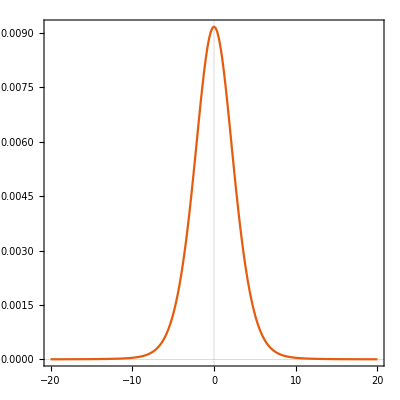

```mathematica
data=ParallelTable[{x,Norm[Quiet[ψsol[x,0]]]^4},{x,-20,20,0.2}];
ListPlot[data,Joined->True,PlotRange->Full,PlotTheme->"Scientific",AspectRatio->1]
```